```mathematica
Clear["Global`*"];
```

```mathematica
a:=2;
Remove[ffund,orthDeriv];
ffund:=Log[(##[[1]]^2+##[[2]]^2)^(1/2)]&;
orthDeriv[f_,xy_]:={-D[f[{x,y}],y],D[f[{x,y}],x]}/.{x->xy[[1]],y->xy[[2]]};
deriv[f_,xy_]:={D[f[{x,y}],x],D[f[{x,y}],y]}/.{x->xy[[1]],y->xy[[2]]};
e1:={1,0};
Remove[x,y];
```

```mathematica
Options[plotRegionStream]={intervalOpt->{-1,1},aOpt->2,noInflowOpt->False,levelFunction->None,plotDomain->None,plotCriticalPoints->True,streamPlotOpt->True};
plotRegionStream[u_,psi_,OptionsPattern[]]:=With[{interval=OptionValue[intervalOpt],
a=OptionValue[aOpt],
noInflow=OptionValue[noInflowOpt],
f=OptionValue[levelFunction],
plotCriticalPoints=OptionValue[plotCriticalPoints],
streamPlot=OptionValue[streamPlotOpt]},(
(*Define the plotting region*)
plotRegion=OptionValue[plotDomain];
If[plotRegion===None,
plotRegion=ImplicitRegion[-a<x<a&&-a<y<a&&interval[[1]]<=Evaluate[psi[{x,y}]]<=interval[[2]],{x,y}],];

(*plot the streamplot*)
If[streamPlot,plts = {StreamPlot[Evaluate[u[{x,y}]],{x,y}∈plotRegion, StreamPoints->{Automatic,Scaled[0.01]},FrameLabel->{Subscript[x, 1],Subscript[x, 2]},
RegionFillingStyle->LightGray,RegionBoundaryStyle->None,StreamColorFunction->"GrayTones",ImageSize->Large,PerformanceGoal->"Quality"(*,StreamScale->{Tiny,All}*)]},
plts = {VectorPlot[Evaluate[u[{x,y}]],{x,y}∈plotRegion, VectorPoints->50,FrameLabel->{Subscript[x, 1],Subscript[x, 2]},
RegionFillingStyle->LightGray,RegionBoundaryStyle->None,VectorColorFunction->"GrayTones",ImageSize->Large,PerformanceGoal->"Quality"(*,StreamScale->{Tiny,All}*)]}];

(*plot boundaries*)
If[noInflow,
If[OptionValue[plotDomain]===None,
AppendTo[plts,Table[ContourPlot[Evaluate[psi[{x,y}]]==level,{x,-a,a},{y,-a,a},ContourStyle->{Black,Opacity[0.5]}],
{level,interval}]],
AppendTo[plts,RegionPlot[plotRegion,PlotStyle->None,BoundaryStyle->{Black,Opacity[0.5]}]]],
boundaryFunc =({D[psi[{dx,dy}],dx],D[psi[{dx,dy}],dy]}/.{dx:>##[[1]],dy:>##[[2]]}).u[##]&;
sigmaRegions=Table[ImplicitRegion[-a<=x<=a&&-a<=y<=a&&symb[boundaryFunc[{x,y}]],{x,y}],{symb,{LessThan[0],GreaterThan[0]}}];
AppendTo[plts, Table[Table[ContourPlot[Evaluate[psi[{x,y}]]==level,{x,y}∈params[[1]],ContourStyle->{params[[2]],Opacity[0.5]}],{params,{{sigmaRegions[[1]],Blue},{sigmaRegions[[2]],Red}}}],
{level,interval}]]];

(*plot critical points*)
If[plotCriticalPoints,
zeros=(NSolve[(Evaluate[u[{x,y}]]=={0,0})&&{x,y}∈plotRegion,{x,y}])[[All,All,2]];AppendTo[plts,ListPlot[zeros,PlotStyle->{Black,PointSize[0.04]}]];
If[f===None,,
(*plot contours*)
AppendTo[plts,ContourPlot[Evaluate[f[{x,y}]],{x,y}∈plotRegion,Contours->f@Transpose[zeros],ContourStyle->Dashed,Mesh->None,ContourShading->None]]];,];

p=Show[plts];
p=Legended[p,Placed[LineLegend[{Red,Black,Blue,{Black,Dashed}},{"Σ^+","Σ^0","Σ^-","level set"}],After]];
p=Legended[p,Placed[PointLegend[{Black},{"critical point"}],After]]
);
p
]
```

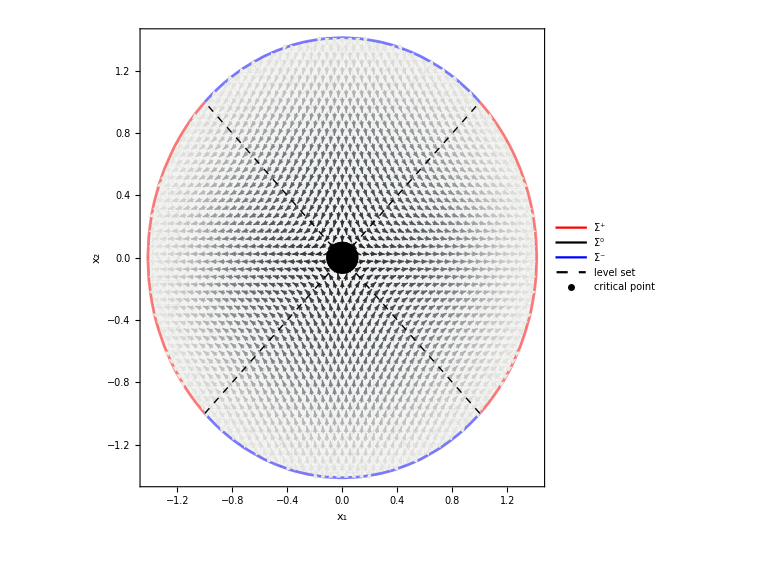

```mathematica
f6=##[[1]]^2-##[[2]]^2&;
u6=deriv[f6,##]&;
levelCircle=##[[1]]^2+##[[2]]^2&;
plotRegionStream[u6,levelCircle,intervalOpt->{-4,2},levelFunction->f6,streamPlotOpt->False]
```

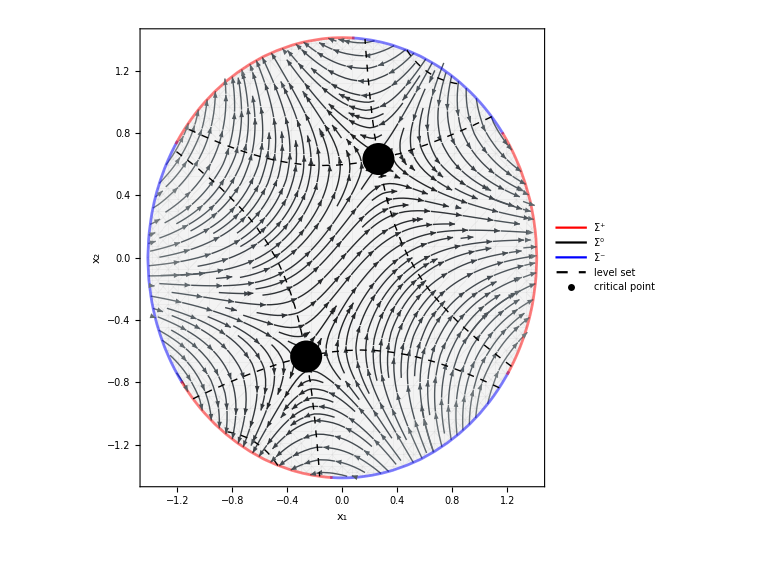

```mathematica
f7=##[[1]]^3-3##[[1]]*##[[2]]^2+##[[1]]+##[[2]] &;
u7=deriv[f7,##]&;
plotRegionStream[u7,levelCircle,intervalOpt->{-4,2},levelFunction->f7]
```

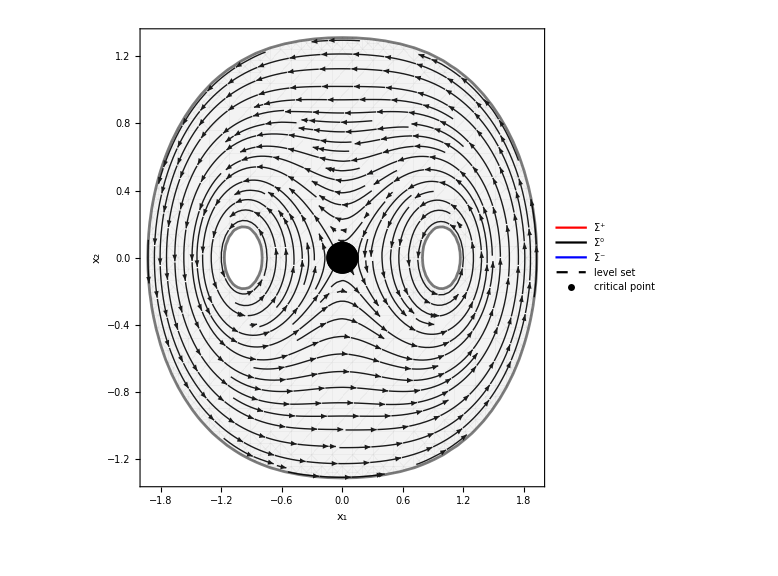

```mathematica
psi1:=ffund[##-e1]+ffund[##+e1]&;
u1:=orthDeriv[psi1,##] &;
plotRegionStream[u1,psi1,noInflowOpt->True]
```

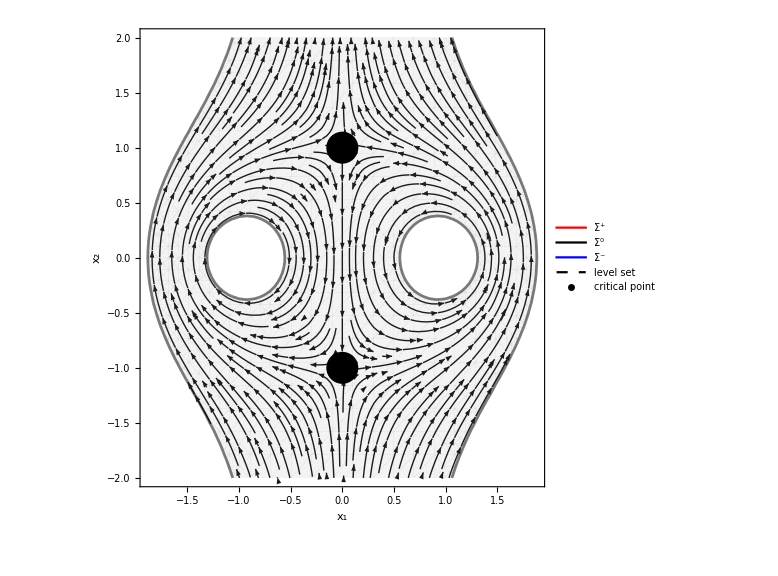

```mathematica
psi2:=ffund[##-e1]-ffund[##+e1]+##[[1]]&;
u2:=orthDeriv[psi2,##] &;
plotRegionStream[u2,psi2,noInflowOpt->True,intervalOpt->{-0.7,0.7}]
```

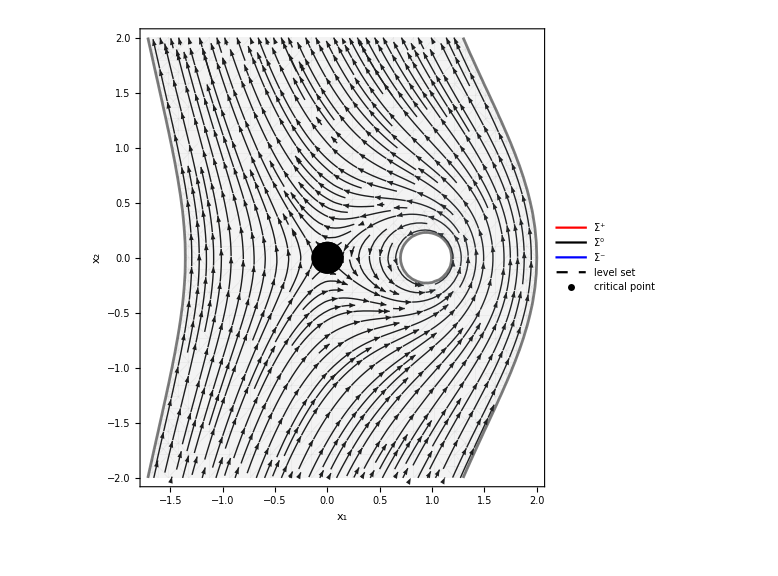

```mathematica
psi3:=ffund[##-e1]+##[[1]]&;
u3:=orthDeriv[psi3,##] &;
plotRegionStream[u3,psi3,noInflowOpt->True,intervalOpt->{-0.5,2}]
```

```mathematica
Animate[StreamPlot[(1-lambda)*u1[{x,y}]+lambda*u2[{x,y}],{x,-a,a},{y,-a,a},FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, StreamPoints->Fine],{lambda,0,1},AnimationRunning->False, AnimationRate->.05]
```

```mathematica
Animate[VectorPlot[(1-lambda)*u1[{x,y}]4+lambda*u2[{x,y}],{x,-a,a},{y,-a,a},FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, VectorPoints->Fine],{lambda,0,1},AnimationRunning->False, AnimationRate->.05]
```

```mathematica
regionOmega=RegionDifference[Disk[{0,0},4],RegionUnion[Disk[{-2,0},1],Disk[{2,0},1]]];
solveDirichlet[uBoundary_]:=With[{LaplaceEquation2D={Laplacian[u[x,y],{x,y}]==0, DirichletCondition[u[x,y]==uBoundary[x,y],True]}},(
NDSolveValue[LaplaceEquation2D,u,{x,y}∈regionOmega][##[[1]],##[[2]]]&)]

uBoundary1=If[#1^2+#2^2>15,0,1]&;
psi4=solveDirichlet[uBoundary1];
u4=orthDeriv[psi4,##]&;
```

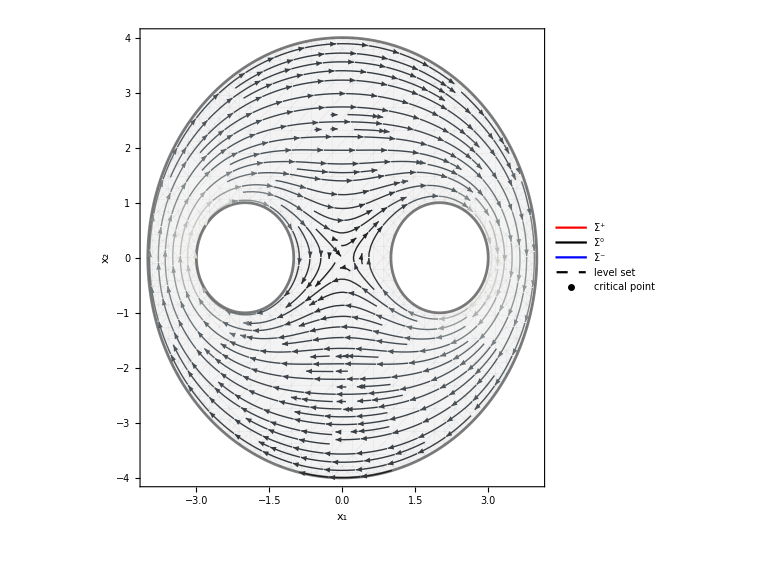

```mathematica
plotRegionStream[u4,psi4,noInflowOpt->True,intervalOpt->{0,1},plotDomain->regionOmega]
```

```mathematica
uBoundary2=If[#1^2+#2^2>15,0,If[#1>0,-1,1]]&;
psi5=solveDirichlet[uBoundary2];
u5=orthDeriv[psi5,##]&;
```

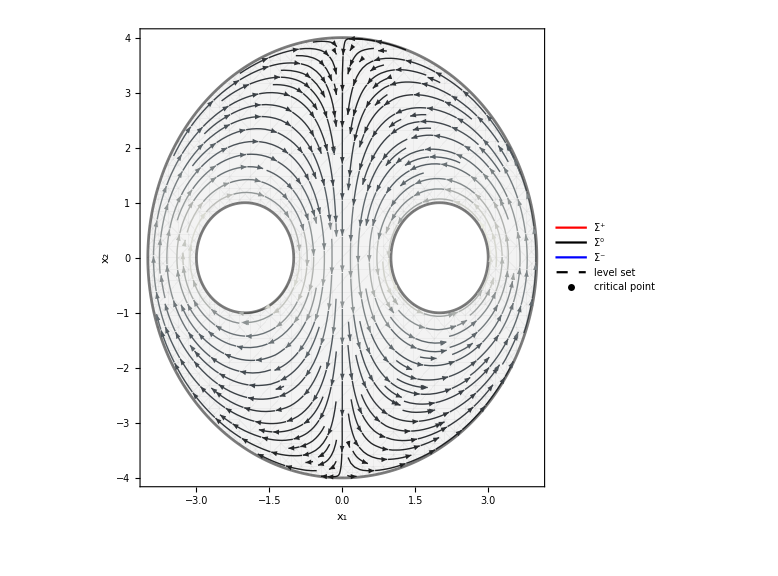

```mathematica
(*StreamPlot[Evaluate[g5[{x,y}]],{x,y}∈regionOmega,FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, StreamPoints->Fine]*)
plotRegionStream[u5,psi5,noInflowOpt->True,intervalOpt->{-1,1},plotDomain->regionOmega,plotCriticalPoints->False]
```

```mathematica
Export["D:\\MasterThesis\\Plots\\n2_hvf_transition_FixedDomain_details05.pdf",Table[plotRegionStream[(lambda*u4[##]+(1-lambda)*u5[##])&,None,noInflowOpt->True,intervalOpt->{0,1},plotDomain->RegionIntersection[regionOmega,Rectangle[{2,-1},{4,1}]],streamPlotOpt->False],{lambda,Subdivide[0.4991,0.501,20]}]];
```

```mathematica
Export["D:\\MasterThesis\\Plots\\n2_hvf_transition_FixedDomain_details07.pdf",Table[plotRegionStream[(lambda*u4[##]+(1-lambda)*u5[##])&,None,noInflowOpt->True,intervalOpt->{0,1},plotDomain->RegionIntersection[regionOmega,Rectangle[{0,-1},{2,1}]],streamPlotOpt->False],{lambda,Subdivide[0.8,0.9,10]}]];
```

```mathematica
Animate[StreamPlot[Evaluate[(1-lambda)*u4[{x,y}]+lambda*u5[{x,y}]],{x,y}∈regionOmega,FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, StreamPoints->Fine],{lambda,0,1},AnimationRunning->False, AnimationRate->.05]
```